```mathematica
iprod[a_,b_]=Dot[Conjugate[a],b];
```

```mathematica
Orthogonalize[{{1,1,1,1},{1,-1,1,-1},{1,-I,1,I},{1,1,I,I}},iprod]
```

{{1/2,1/2,1/2,1/2},{1/2,-1/2,1/2,-1/2},{0,-ⅈ/(√2),0,ⅈ/(√2)},{1/2-ⅈ/2,0,-1/2+ⅈ/2,0}}

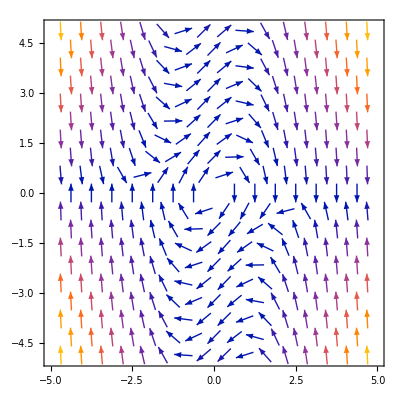

```mathematica
VectorPlot[{y,-x+(1-x^2)*y},{x,-5,5},{y,-5,5}]
```

```mathematica
f[x_,y_] := {y,-x+(1-x^2)*y}
```

```mathematica
{xsoln,ysoln}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==0,y[0]==0.5},{x,y},{t,0,10}];
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5}];
curve=ParametricPlot[{xsoln[t],ysoln[t]},{t,0,10},PlotStyle->{Red,Thickness[Medium]},PlotRange->All];
Show[field,curve]
```

NDSolveValue::underdet: There are more dependent variables, {x[t],y[t]}, than equations, so the system is underdetermined.

Set::shape: Lists {xsoln,ysoln} and NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==0,y[0]==0.5},{x,y},{t,0,10}] are not the same shape.

-Graphics-

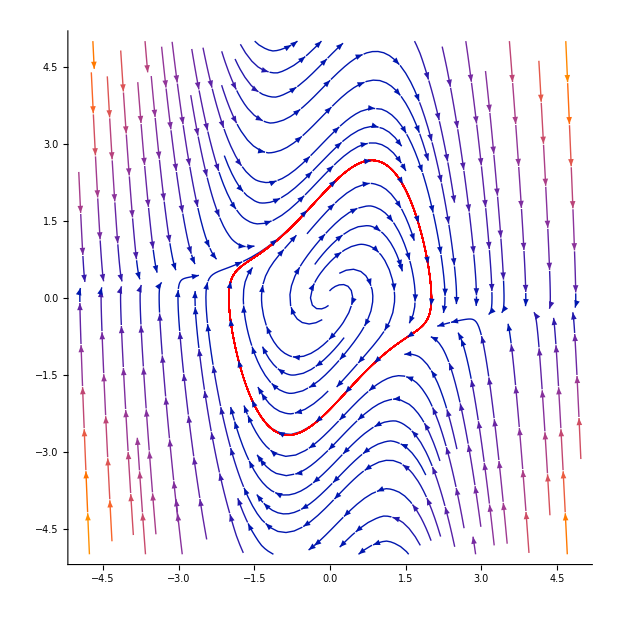

```mathematica
f[{x_,y_}]:={y,-x + (1-x^2)*y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln,ysoln}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==0,y[0]==2.17},{x,y},{t,0,100}];
curve=ParametricPlot[{xsoln[t],ysoln[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[{field,curve}]
```

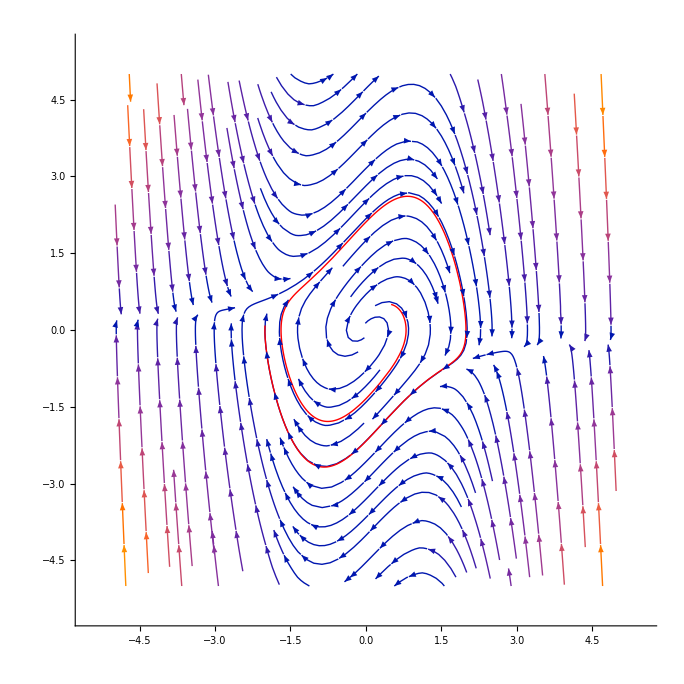

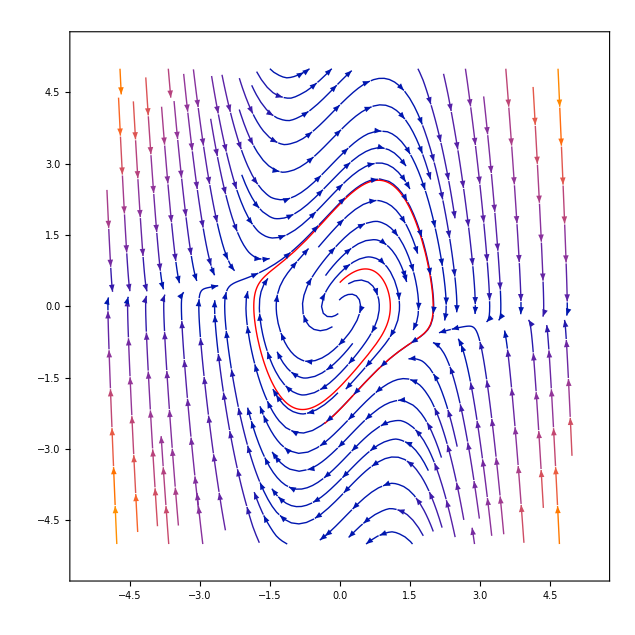

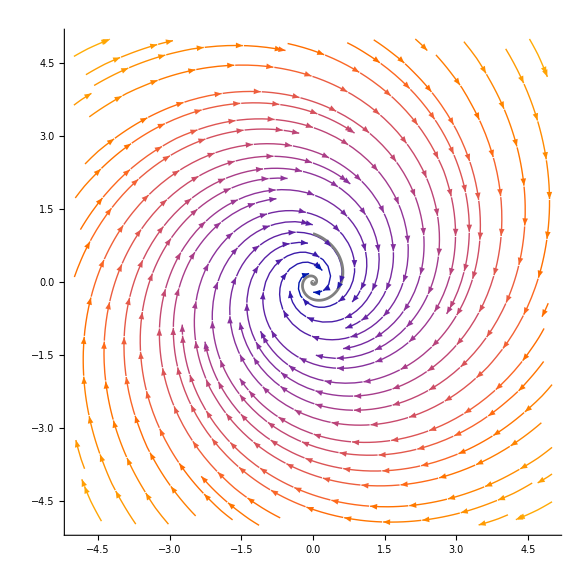

```mathematica
field=StreamPlot[{-x+3y,-3x-y},{x,-5,5},{y,-5,5},Frame->False,Axes->True];
curve1 = ParametricPlot[{Exp[-t]*Sin[3t],Exp[-t]*Cos[3t]},{t,0,10},PlotStyle->{Red,Dashed}];
curve2 =  ParametricPlot[{Exp[-(t-1)]*Sin[3*(t-1)],Exp[-1*(t-1)]*Cos[3(t-1)]},{t,1,11},PlotStyle->{Gray}];
Show[field,curve2]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/2_6_5b.pdf",%137,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/2_6_5b.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/2_6_5a.pdf",%112,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/2_6_5a.pdf

```mathematica
field=StreamPlot[{-x+3y,-3x-y},{x,-5,5},{y,-5,5},Frame->False,Axes->True];
curve1 = ParametricPlot[{Exp[-t]*Sin[3t],Exp[-t]*Cos[3t]},{t,0,10},PlotStyle->{Red,Dashed}];
Show[field,curve2]
```

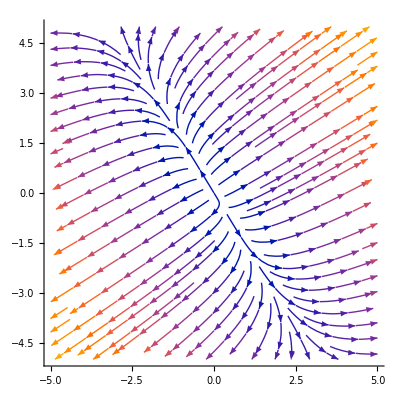

```mathematica
f[{x_,y_}]:={2x+y,x+y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln,ysoln}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==1,y[0]==1},{x,y},{t,0,100}];
curve=ParametricPlot[{xsoln[t],ysoln[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[{field,curve}]
Show[Plot[xsoln[t],{t,0,10}],Plot[ysoln[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_10_a.pdf",%170,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_10_a.pdf

-Graphics-

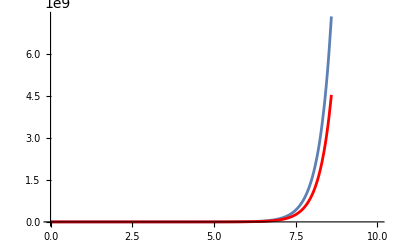

```mathematica
f[{x_,y_}]:={2x+y,x+y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln,ysoln}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==1.3,y[0]==0.7},{x,y},{t,0,100}];
curve=ParametricPlot[{xsoln[t],ysoln[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[{field,curve}]
Show[Plot[xsoln[t],{t,0,10}],Plot[ysoln[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_10_b.pdf",%183,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_10_b.pdf

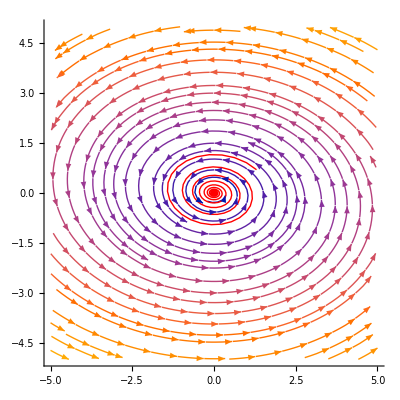

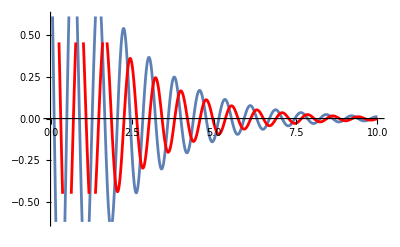

```mathematica
f[{x_,y_}]:={-x-11y,6x}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln,ysoln}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==1.3,y[0]==0.7},{x,y},{t,0,100}];
curve=ParametricPlot[{xsoln[t],ysoln[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[{field,curve}]
Show[Plot[xsoln[t],{t,0,10}],Plot[ysoln[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_13_b.pdf",%198,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_13_b.pdf

-Graphics-

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_13_a.pdf",%190,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_1_13_a.pdf

```mathematica
m = {{0,1},{1,0}};
v = (1/Sqrt[2]){{1},{1}};
w = (1/Sqrt[2]){{1},{-1}};
```

```mathematica
m.v
```

{{1/(√2)},{1/(√2)}}

```mathematica
Dot[w,m.v]
```

Dot::dotsh: Tensors {{1/(√2)},{-1/(√2)}} and {{1/(√2)},{1/(√2)}} have incompatible shapes.

{{1/(√2)},{-1/(√2)}}.{{1/(√2)},{1/(√2)}}

```mathematica
iprod[{1/3(I - Sqrt[3]),1/3(1+2I)},{1-I,2+2I}]
```

(2-(2 ⅈ)/3)+(1/3-ⅈ/3) (-ⅈ-√3)

```mathematica
Simplify[%]
```

(5/3-ⅈ)-(1-ⅈ)/(√3)

```mathematica
Simplify[iprod[{1/3(1-2I),1/3(I+Sqrt[3])},{1-I,2+2I}]]
```

(5/3-ⅈ/3)+(2+2 ⅈ)/(√3)

```mathematica
Simplify[iprod[{1/3(I - Sqrt[3]),1/3(1+2I)},{1+I,2I}]]
```

(-1/3-ⅈ/3) ((-3+2 ⅈ)+√3)

```mathematica
Simplify[Im[(-1/3-ⅈ/3) ((-3+2 ⅈ)+√3)]]
```

1/3-1/(√3)

```mathematica
Simplify[Re[(-1/3-ⅈ/3) ((-3+2 ⅈ)+√3)]]
```

5/3-1/(√3)

```mathematica
N[(-1/3-ⅈ/3) ((-3+2 ⅈ)+√3)]
```

1.08932-0.244017 ⅈ

```mathematica
Re[1.0893163974770408-0.24401693585629236 ⅈ]
```

1.08932

```mathematica
Re[Simplify[iprod[{1/3(1-2I),1/3(I+Sqrt[3])},{1+I,2I}]]]
Im[Simplify[iprod[{1/3(1-2I),1/3(I+Sqrt[3])},{1+I,2I}]]]
```

1/3

1+2/(√3)

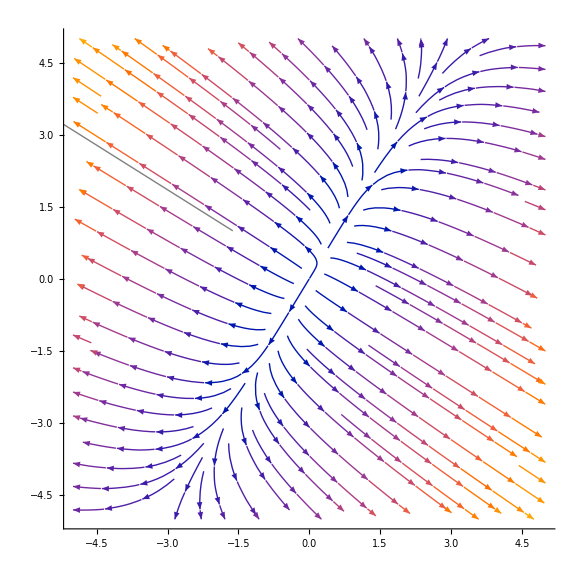

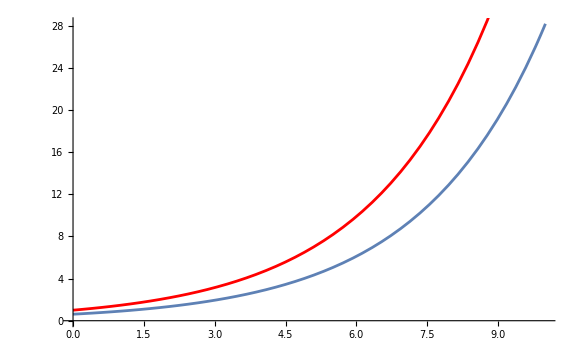

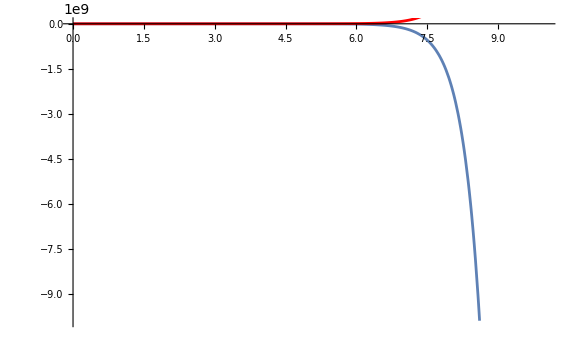

```mathematica
f[{x_,y_}]:={2x-y,-x+y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==((Sqrt[5]-1)/2),y[0]==1},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==((-Sqrt[5]-1)/2),y[0]==1},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[xsoln1[t],{t,0,10}],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10}],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8db.pdf",%314,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8db.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8da.pdf",%303,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8da.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8c.pdf",%292,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_8c.pdf

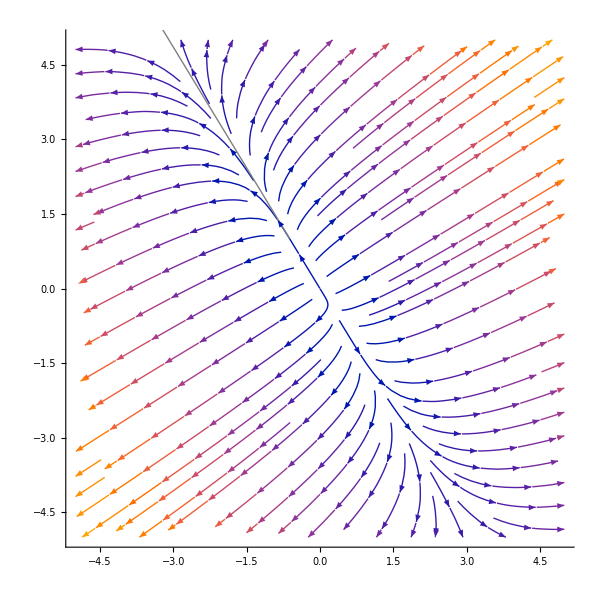

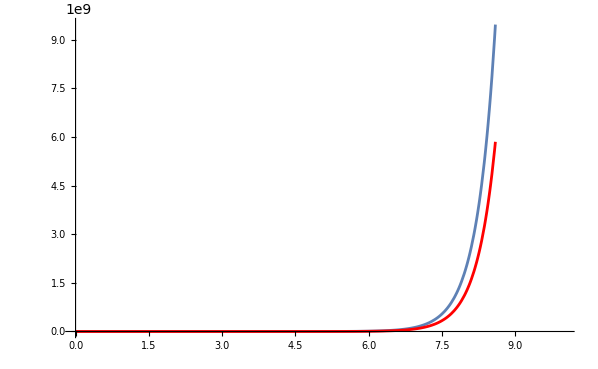

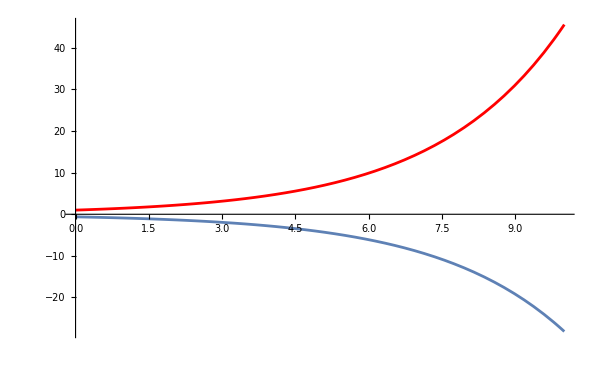

```mathematica
f[{x_,y_}]:={2x+y,x+y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==((1+Sqrt[5])/2),y[0]==1},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==((-Sqrt[5]+1)/2),y[0]==1},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[xsoln1[t],{t,0,10}],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9db.pdf",%380,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9db.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9a.pdf",%369,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9a.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9c.pdf",%358,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/Homework/images/3_2_9c.pdf

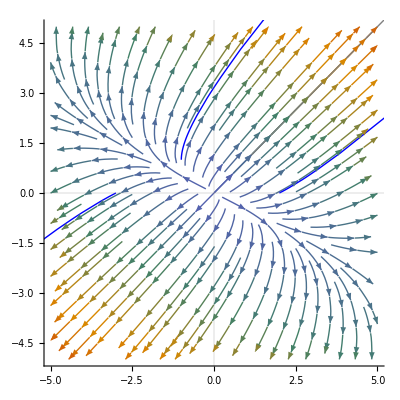

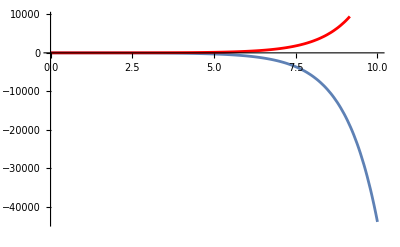

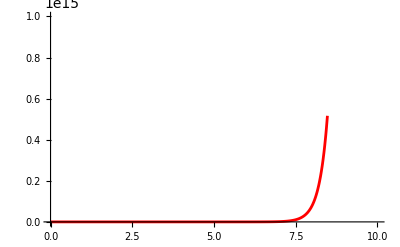

```mathematica
f[{x_,y_}]:={2x + 2y,x+3y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True,PlotTheme->"Scientific"];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-2,y[0]==1},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==1,y[0]==1},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln3,ysoln3}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-1,y[0]==1},{x,y},{t,0,100}];
curve3=ParametricPlot[{xsoln3[t],ysoln3[t]},{t,0,7},PlotStyle->{Blue,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln4,ysoln4}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==2,y[0]==0},{x,y},{t,0,100}];
curve4=ParametricPlot[{xsoln4[t],ysoln4[t]},{t,0,7},PlotStyle->{Blue,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln5,ysoln5}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-3,y[0]==0},{x,y},{t,0,100}];
curve5=ParametricPlot[{xsoln5[t],ysoln5[t]},{t,0,7},PlotStyle->{Blue,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2,curve3,curve4,curve5]
Show[Plot[xsoln1[t],{t,0,10},PlotRange->All],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->Full],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

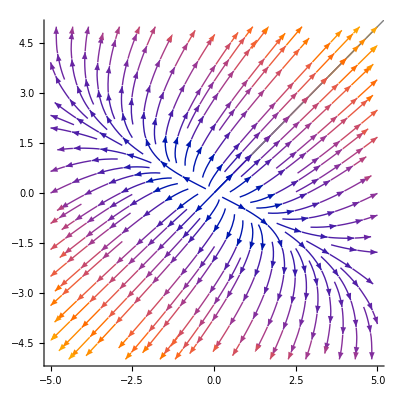

-Graphics-

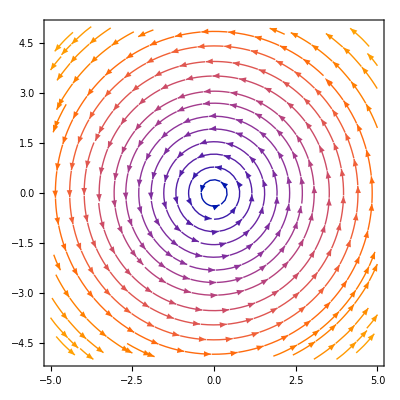

```mathematica
StreamPlot[{-y,x},{x,-5,5},{y,-5,5}]
```

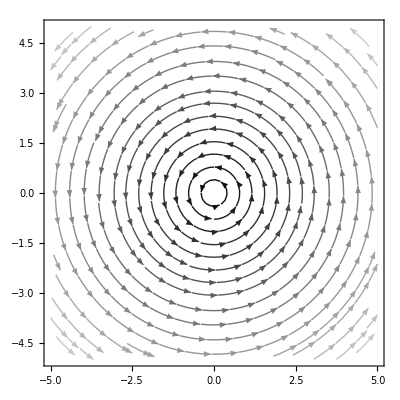

```mathematica
StreamPlot[{-y,x},{x,-5,5},{y,-5,5},PlotTheme->"Monochrome"]
```

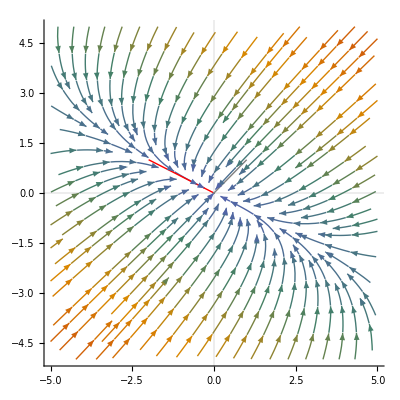

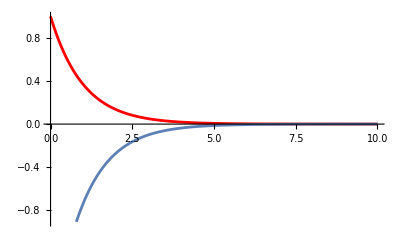

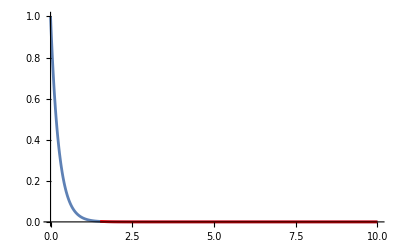

```mathematica
f[{x_,y_}]:={-2x-2y,-x-3y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True,PlotTheme->"Scientific"];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-2,y[0]==1},{x,y},{t,-100,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==1,y[0]==1},{x,y},{t,-100,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[ysoln1[t],{t,0,10},PlotStyle->Red,PlotRange->All],Plot[xsoln1[t],{t,0,10}]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

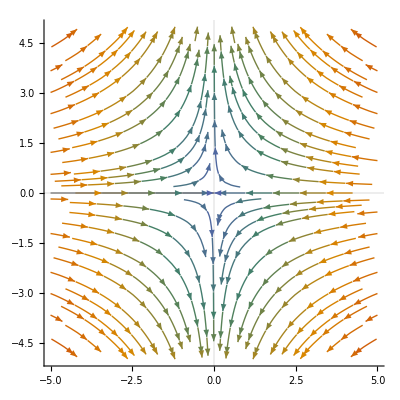

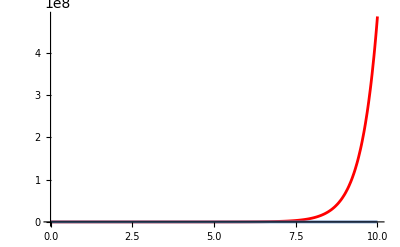

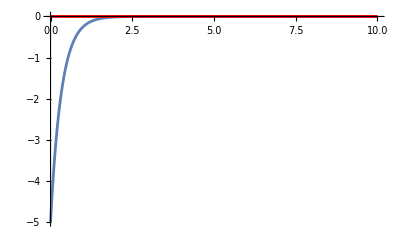

```mathematica
f[{x_,y_}]:={-3x,2y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True,PlotTheme->"Scientific"];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==0,y[0]==1},{x,y},{t,-100,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-5,y[0]==0},{x,y},{t,-100,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[ysoln1[t],{t,0,10},PlotStyle->Red,PlotRange->All],Plot[xsoln1[t],{t,0,10}]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

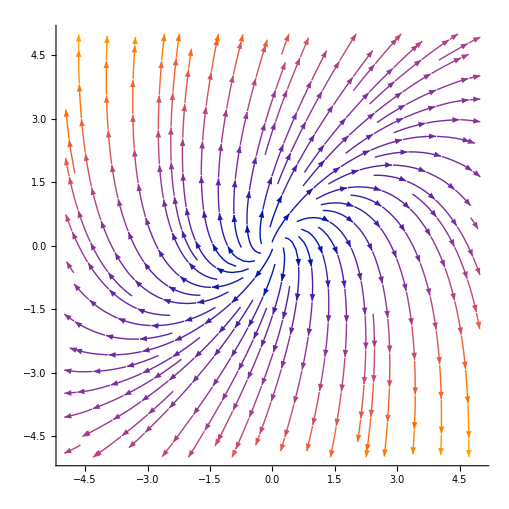

```mathematica
StreamPlot[{2x + 2y,-4x + 6y},{x,-5,5},{y,-5,5},Frame->False,Axes->True]
```

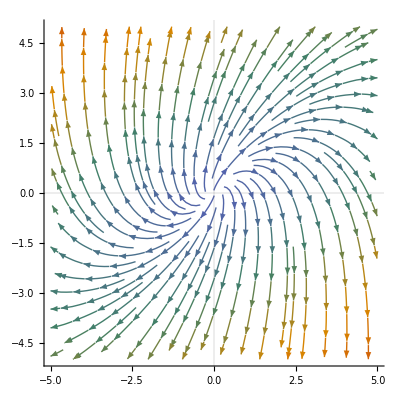

```mathematica
StreamPlot[{2 x+2 y,-4 x+6 y},{x,-5,5},{y,-5,5},PlotTheme->"Scientific",Frame->False,Axes->True]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/complex_eigenvalues_vector_field.pdf",%4,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/complex_eigenvalues_vector_field.pdf

```mathematica
A = (1/Sqrt[6]){{1,-Sqrt[3],Sqrt[2]},{-2,0,Sqrt[2]},{1,Sqrt[3],Sqrt[2]}}
```

{{1/(√6),-1/(√2),1/(√3)},{-√(2/3),0,1/(√3)},{1/(√6),1/(√2),1/(√3)}}

```mathematica
Inverse[A]
```

{{1/(√6),-√(2/3),1/(√6)},{-1/(√2),0,1/(√2)},{1/(√3),1/(√3),1/(√3)}}

```mathematica
Transpose[A] == Inverse[A]
```

True

```mathematica
B = (1/2*Sqrt[2]){{2,2*I},{-2*I,2}}
```

{{√2,ⅈ √2},{-ⅈ √2,√2}}

```mathematica
ConjugateTranspose[B]==B
```

True

```mathematica
ConjugateTranspose[B]==Inverse[B]
```

Inverse::sing: Matrix {{√2,ⅈ √2},{-ⅈ √2,√2}} is singular.

{{√2,ⅈ √2},{-ⅈ √2,√2}}==Inverse[{{√2,ⅈ √2},{-ⅈ √2,√2}}]

```mathematica
cc = {{I,1,I},{2,I,0},{I,1,-I}};
ConjugateTranspose[cc]==Inverse[cc]
ConjugateTranspose[cc]==cc
Transpose[cc] == Inverse[cc]
```

False

False

False

```mathematica
ee= {{0,-I},{I,0}};
ConjugateTranspose[ee]==Inverse[ee]
```

True

```mathematica
A = (1/4){{3,Sqrt[6],-1},{-Sqrt[6],2,-Sqrt[6]},{-1,Sqrt[6],3}}
Eigenvectors[A]
```

{{3/4,(√(3/2))/2,-1/4},{-(√(3/2))/2,1/2,-(√(3/2))/2},{-1/4,(√(3/2))/2,3/4}}

```mathematica
MatrixForm[A]
```

(3/4 | (√(3/2))/2 | -1/4
-(√(3/2))/2 | 1/2 | -(√(3/2))/2
-1/4 | (√(3/2))/2 | 3/4)

```mathematica
MatrixForm[{{-1,0,1},{1,ⅈ √2,1},{1,-ⅈ √2,1}}]
```

(-1 | 0 | 1
1 | ⅈ √2 | 1
1 | -ⅈ √2 | 1)

```mathematica
DiagonalMatrix[A]
```

DiagonalMatrix::nosmat: A structured diagonal matrix could not be constructed from {{3/4,(√(3/2))/2,-1/4},{-(√(3/2))/2,1/2,-(√(3/2))/2},{-1/4,(√(3/2))/2,3/4}}.

DiagonalMatrix[{{3/4,(√(3/2))/2,-1/4},{-(√(3/2))/2,1/2,-(√(3/2))/2},{-1/4,(√(3/2))/2,3/4}}]

```mathematica
Det[A]
```

1

```mathematica
S = (1/2){{1,2,-1},{2,-2,2},{-1,2,1}};
CharacteristicPolynomial[S,x]
```

-2+3 x-x^3

```mathematica
Eigenvalues[S]
```

{-2,1,1}

```mathematica
Eigenvectors[S]
```

{{1,-2,1},{-1,0,1},{2,1,0}}

{{1/2,1,-1/2},{-2,2,-2},{-1/2,1,1/2}}

```mathematica
S.{1,-2,1}
```

{-2,4,-2}

```mathematica
Inverse[{{3/5,4/5,0},{-4/5,3/5,0},{0,0,1}}]
```

{{3/5,-4/5,0},{4/5,3/5,0},{0,0,1}}

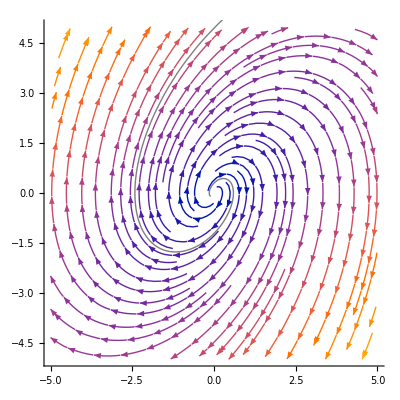

```mathematica
f[{x_,y_}]:={2y,-3x+2y}
field=StreamPlot[f[{x,y}],{x,-5,5},{y,-5,5},Frame->False,Axes->True];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==0.1,y[0]==0.1},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-0.1,y[0]==-0.1},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[xsoln1[t],{t,0,10}],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/positive_real_part.pdf",%55,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/positive_real_part.pdf

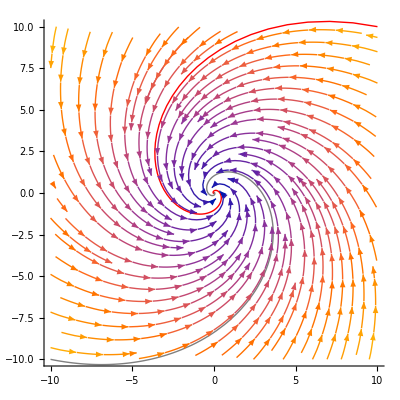

```mathematica
f[{x_,y_}]:={-2x-3y,3x-2y}
field=StreamPlot[f[{x,y}],{x,-10,10},{y,-10,10},Frame->False,Axes->True];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==10,y[0]==10},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==-10,y[0]==-10},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[xsoln1[t],{t,0,10}],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/negative_real_part.pdf",%65,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/negative_real_part.pdf

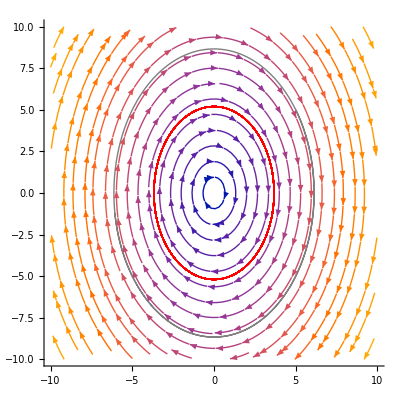

```mathematica
f[{x_,y_}]:={y,-2x}
field=StreamPlot[f[{x,y}],{x,-10,10},{y,-10,10},Frame->False,Axes->True];
{xsoln1,ysoln1}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==3,y[0]==3},{x,y},{t,0,100}];
curve1=ParametricPlot[{xsoln1[t],ysoln1[t]},{t,0,100},PlotStyle->{Red,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
{xsoln2,ysoln2}=NDSolveValue[{{x'[t],y'[t]}==f[{x[t],y[t]}],x[0]==5,y[0]==5},{x,y},{t,0,100}];
curve2=ParametricPlot[{xsoln2[t],ysoln2[t]},{t,0,7},PlotStyle->{Gray,Thickness[Medium]},PlotRange->All,Frame->False,Axes->True];
Show[field,curve1,curve2]
Show[Plot[xsoln1[t],{t,0,10}],Plot[ysoln1[t],{t,0,10},PlotStyle->Red]]
Show[Plot[xsoln2[t],{t,0,10},PlotRange->All],Plot[ysoln2[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/zero_real_part.pdf",%75,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/zero_real_part.pdf